# ITER ECH with linear Slab Profiles

## Open Additional files:

## Get dispersion routines by evaluating Disper.nb Get plotting and printing routines by evaluating PlotPack.nb Set Parameters by opening a Parameter Window Note: Slab profile models defined in initialization cells at the bottom of this notebook.

## First Do Cold Plasma

### Plot Real and Imaginary parts of nx from 2nd order warm plasma dispersion relation (i.e. E_‖≡0)

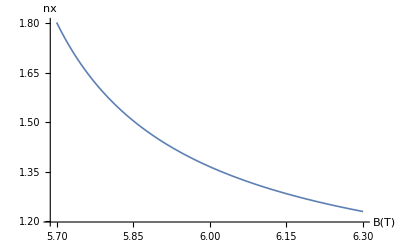

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=5.7

xmax=6.3

```mathematica
nPerpCold[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
     ColdDis0[freq,ne,b,nz,etaList]]
nt=Table[{x,nPerpCold[x]},{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
PPComplexListPlot[nt,"B(T)","nx"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx^2 from 4nd order cold plasma dispersion relation (Fast and Slow roots)

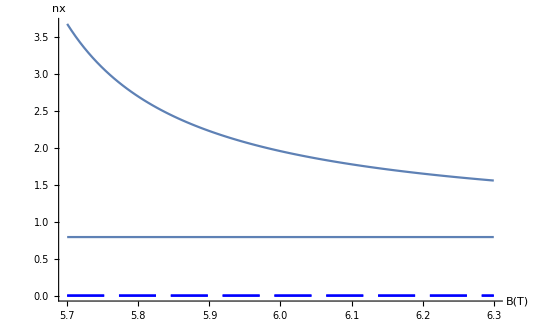

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=5.7

xmax=6.3

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		nxSqColdDisFS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B(T)","nx"];
g2=PPComplexListPlot[nS,"B(T)","nx"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Fast and Slow roots)

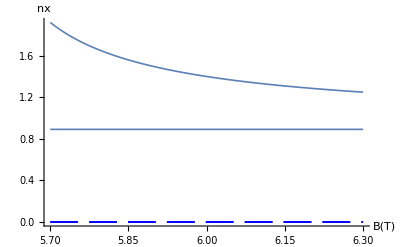

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=5.7

xmax=6.3

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		nxColdDisFS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B(T)","nx"];
g2=PPComplexListPlot[nS,"B(T)","nx"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

### Plot Real and Imaginary parts of nx^2 from 4nd order cold plasma dispersion relation (Plus and Minus roots)

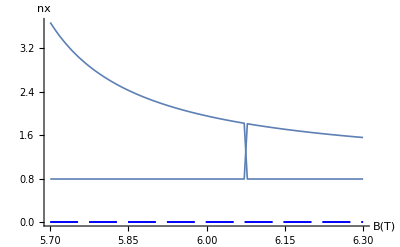

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=5.7

xmin=5.7

nz=0.6

etaList={0.,1.,0.,0.,0.}

xmin=4.38

xmin=4.38

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
	nxSqColdDisPM[freq,ne,b,nz,etaList]]
nt2PM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦2⟧}];
nM=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B(T)","nx"];
g2=PPComplexListPlot[nM,"B(T)","nx"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmin}];
```

### Plot Real and Imaginary parts of nx from 4nd order cold plasma dispersion relation (Plus and Minus roots)

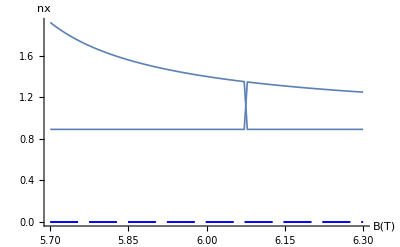

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=5.7

xmax=6.3

```mathematica
nPerp2PM[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
	nxColdDisPM[freq,ne,b,nz,etaList]]
nt2PM=Table[Flatten[{x,nPerp2PM[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nP=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦2⟧}];
nM=Transpose[{Transpose[nt2PM]⟦1⟧,Transpose[nt2PM]⟦3⟧}];
g1=PPComplexListPlot[nP,"B(T)","nx"];
g2=PPComplexListPlot[nM,"B(T)","nx"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

## Now Warm Plasma Stuff

### Plot Real and Imaginary parts of nx from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=5.7

xmax=6.3

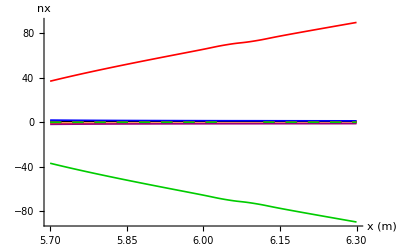

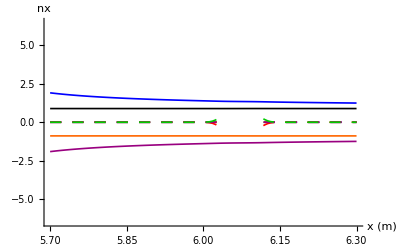

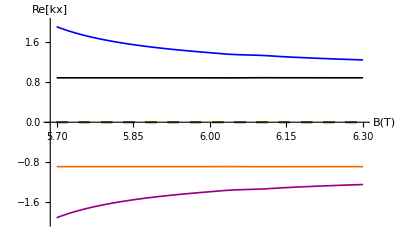

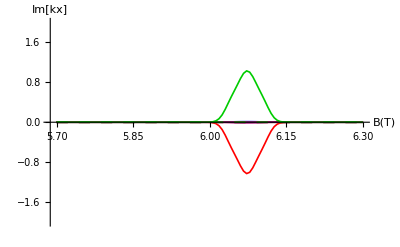

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-6.5,6.5}]
ComplexVectorListPlot[rootsRe,"B(T)", "Re[kx]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "B(T)", "Im[kx]", PlotRange->{-2.,2.}]
```

### Plot Real and Imaginary parts of nx^2 from 6th order warm plasma dispersion relation (expanded to 2nd order in k_⌊ρ)

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

TList={1.,1.,0.,0.,0.,0.}

modelList={1,1,0,0,0,0}

xmin=5.7

xmax=6.3

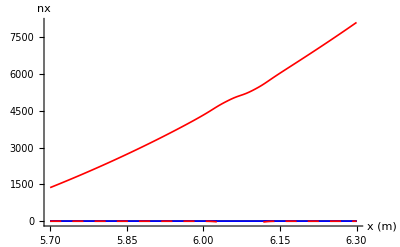

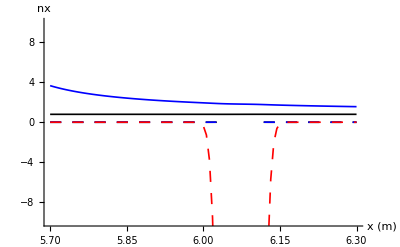

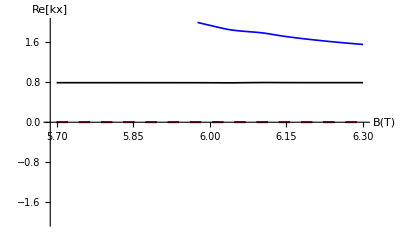

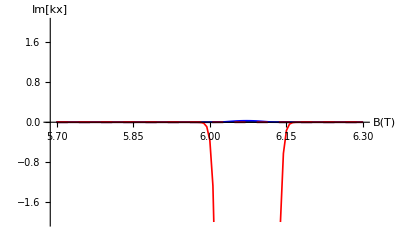

```mathematica
nPerpWarm3[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis2[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm3[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TList, modelList,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-10.,10.}]
ComplexVectorListPlot[rootsRe, "B(T)", "Re[kx]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm, "B(T)", "Im[kx]", PlotRange->{-2.,2.}]
```

## Narrow to look near cyclotron resonance, B = 6.073T

```mathematica
xmin=5.7;
xmax=6.3;
nz  =0.2;
```

```mathematica
nPerp2FS[x_]:=Module[{ne,b,x0},x0=x;
ne=nprof[x0];
b=bprof[x0];
		nxColdDisFS[freq,ne,b,nz,etaList]]
nt2FS=Table[Flatten[{x,nPerp2FS[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
nF=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦2⟧}];
nS=Transpose[{Transpose[nt2FS]⟦1⟧,Transpose[nt2FS]⟦3⟧}];
g1=PPComplexListPlot[nF,"B(T)","nx"];
g2=PPComplexListPlot[nS,"B(T)","nx"];
Show[{g1,g2},PlotRange->All]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,xmin,xmax}];
```

-Graphics-

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

xmin=5.7

xmax=6.3

## Warm Plasma

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TXmin,TXmax,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-6.5,6.5}]
ComplexVectorListPlot[rootsRe, "B(T)", "Re[kx]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm,"B(T)", "Im[kx]", PlotRange->{-2.,2.}]
```

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

TXmin=0.1

TXmax=0.1

xmin=5.7

xmax=6.3

-Graphics-

-Graphics-

-Graphics-

-Graphics-

### Find the X and O modes

```mathematica
nxwarm[[1]]
```

{5.7,0.89015,1.91426,36.9787,-0.89015,-1.91426,-36.9787}

### O - mode is root 1 (cold plasma plus root), X- mode is root 2 (cold plasma minus root)

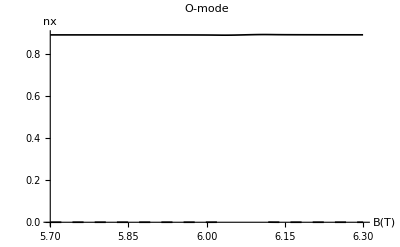

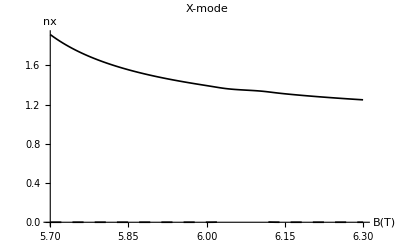

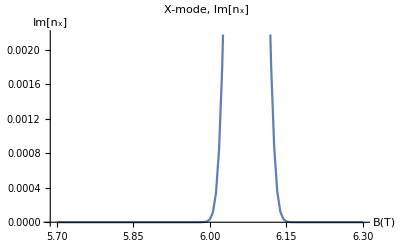

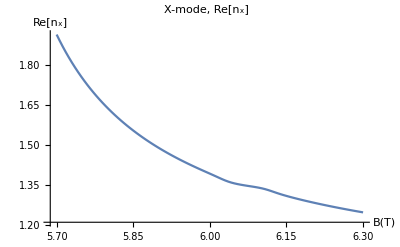

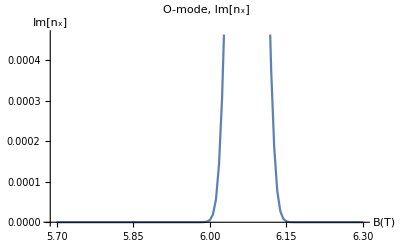

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=0.2

etaList={0.,1.,0.,0.,0.}

TXmin=0.1

TXmax=0.1

xmin=5.7

xmax=6.3

```mathematica
OModeVec=Transpose[{Transpose[nxwarm][[1]],Transpose[nxwarm][[2]]}];
XModeVec=Transpose[{Transpose[nxwarm][[1]],Transpose[nxwarm][[3]]}];
gOMV=ComplexVectorListPlot[OModeVec,"B(T)","nx",PlotLabel->"O-mode"];
gXMV=ComplexVectorListPlot[XModeVec,"B(T)","nx",PlotLabel->"X-mode"];
Show[gOMV,PlotRange->All, AxesOrigin->{xmin,0.}]
Show[gXMV,PlotRange->All, AxesOrigin->{xmin,0.}]
XModeVecRe=Transpose[{Transpose[nxwarm][[1]],Re[Transpose[nxwarm][[3]]]}];OModeVecRe=Transpose[{Transpose[nxwarm][[1]],Re[Transpose[nxwarm][[2]]]}];
XModeVecIm=Transpose[{Transpose[nxwarm][[1]],Im[Transpose[nxwarm][[3]]]}];OModeVecIm=Transpose[{Transpose[nxwarm][[1]],Im[Transpose[nxwarm][[2]]]}];
ListPlot[XModeVecIm, Joined->True, AxesLabel->{"B(T)", "Im[n_x]"},PlotLabel->"X-mode,   Im[n_x]"]
ListPlot[XModeVecRe, Joined->True, AxesLabel->{"B(T)", "Re[n_x]"},PlotLabel->"X-mode,   Re[n_x]"]
ListPlot[OModeVecIm, Joined->True, AxesLabel->{"B(T)", "Im[n_x]"},PlotLabel->"O-mode,   Im[n_x]"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TXmin,TXmax,xmin,xmax}];
```

## Compare against Fortran damp_fund _ECH()

### X-mode (slow), from Fortran selected values of (x, ki ) for X - mode. N.B. Bres = 6.073T

#### RAYS Mathematica

6.0048    1.3948     0.0180              1.37347+0.0159911 ⅈ
6.0568    1.3570     0.0257              1.35049+0.024667 ⅈ
6.0710    1.3499    0.0253               1.346+0.0249238 ⅈ
6.1105    1.3274    0.0195               1.33468+0.0207991 ⅈ
6.1611    1.3005   0.0059               1.31492+0.00745537 ⅈ

```mathematica
nPerpWarm6[6.0048][[2]]
nPerpWarm6[6.0568][[2]]
nPerpWarm6[6.0710][[2]]
nPerpWarm6[6.1105][[2]]
nPerpWarm6[6.1611][[2]]
```

1.3894+0.0000914063 ⅈ

1.3534+0.0099984 ⅈ

1.34868+0.0112132 ⅈ

1.3342+0.00414747 ⅈ

1.3043+4.97229×10^-7 ⅈ

It looks like agreement is not too bad

### O-mode (fast), from Fortran selected values of (x, ki ). N.B. Bres = 6.073T

```mathematica
nPerpWarm6[6.0015][[1]]
nPerpWarm6[6.0553][[1]]
nPerpWarm6[6.0687][[1]]
nPerpWarm6[6.1090][[1]]
nPerpWarm6[6.1493][[1]]
```

0.889528+7.49081×10^-6 ⅈ

0.88933+0.00185653 ⅈ

0.890057+0.0021512 ⅈ

0.891766+0.000924569 ⅈ

0.890981+2.46752×10^-6 ⅈ

#### RAYS Mathematica

6.0015    0.8903    0.0026               0.887034+0.00264938 ⅈ
6.0553    0.8903    0.0046               0.889326+0.00474948 ⅈ
6.0687    0.8903   0.0047                0.890112+0.00485706 ⅈ
6.1090    0.8903   0.0041                0.892315+0.00418004 ⅈ
6.1493    0.8903   0.0022                0.893537+0.00226901 ⅈ

Agreement is better than for the X-mode, probably because the damping is weaker

## Optical depth

X - mode

```mathematica
kiXModeVec=Transpose[{Transpose[nxwarm][[1]],k0*Im[Transpose[nxwarm][[3]]]}];
α=TrapezInt[kiXModeVec]
1-Exp[-2α]
```

2.67673

0.995268

In fortran, RAYS total damping = 0.9954. Pretty good

O - mode

```mathematica
kiXModeVec=Transpose[{Transpose[nxwarm][[1]],k0*Im[Transpose[nxwarm][[2]]]}];
α=TrapezInt[kiXModeVec]
1-Exp[-2α]
```

0.515428

0.643299

In fortran, RAYS total damping = 0.6440 . Pretty good

## What happens if nz < 0

```mathematica
nz=-0.2
xmin=5.7;
xmax=6.3;
```

-0.2

### Warm Plasma

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=-0.2

etaList={0.,1.,0.,0.,0.}

TXmin=0.1

TXmax=0.1

xmin=5.7

xmax=6.3

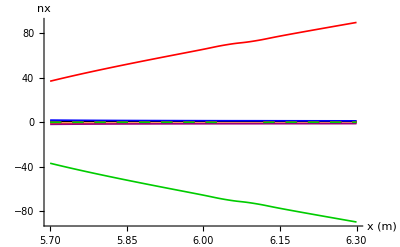

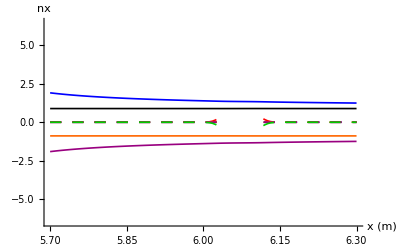

-Graphics-

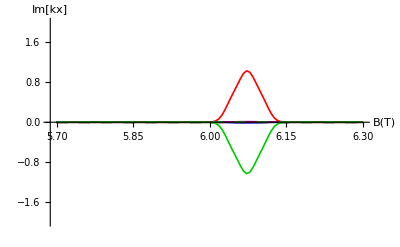

```mathematica
nPerpWarm6[x_]:=Module[{ne,te,b,x0,TL},
		x0=x;
     ne=nprof[x0];
b=bprof[x0];
	  TL=tprof[x0] *TList;
	  WarmDis6[freq,ne,b,nz,etaList,TL]]

nxwarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
roots=rootSort[nxwarm];
rootsRe=Table[Flatten[{roots[[i]][[1]],Table[Re[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

rootsIm=Table[Flatten[{roots[[i]][[1]],Table[Im[roots[[i]][[j]]],{j,2,Length[roots[[i]]]}]}],{i,Length[roots]}];

g6=ComplexVectorListPlot[roots,"x (m)","nx"];
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TXmin,TXmax,xmin,xmax}];
Show[g6,PlotRange->All]
Show[g6,PlotRange->{-6.5,6.5}]
ComplexVectorListPlot[rootsRe, "B(T)", "Re[kx]", PlotRange->{-2.,2.}]
ComplexVectorListPlot[rootsIm,"B(T)", "Im[kx]", PlotRange->{-2.,2.}]
```

### Find the X and O modes

```mathematica
nxwarm[[1]]
```

{5.7,0.89015,1.91426,36.9787,-0.89015,-1.91426,-36.9787}

### X - mode is root 2, O - mode is root 1

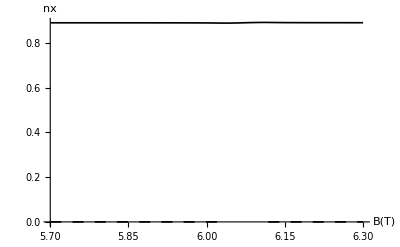

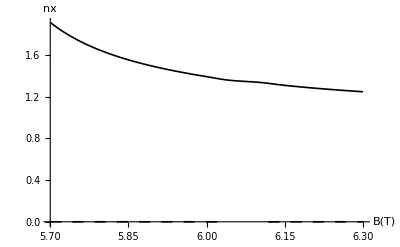

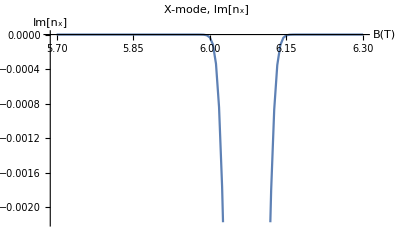

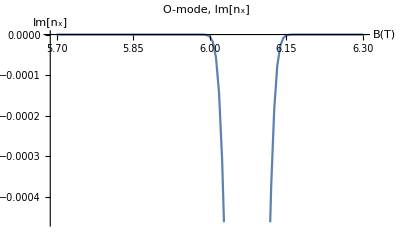

dataSet=Slab 170HHz

xProfileMin=4.2

xProfileMax=7.5

nXmin=6.24×10^19

nXmax=6.24×10^19

BXmin=4.2

BXmax=7.5

freq=170000

nz=-0.2

etaList={0.,1.,0.,0.,0.}

TXmin=0.1

TXmax=0.1

xmin=5.7

xmax=6.3

```mathematica
OModeVec=Transpose[{Transpose[nxwarm][[1]],Transpose[nxwarm][[2]]}];
XModeVec=Transpose[{Transpose[nxwarm][[1]],Transpose[nxwarm][[3]]}];
gOMV=ComplexVectorListPlot[OModeVec,"B(T)","nx"];
gXMV=ComplexVectorListPlot[XModeVec,"B(T)","nx"];
Show[gOMV,PlotRange->All, AxesOrigin->{xmin,0.}]
Show[gXMV,PlotRange->All, AxesOrigin->{xmin,0.}]
XModeVecIm=Transpose[{Transpose[nxwarm][[1]],Im[Transpose[nxwarm][[3]]]}];OModeVecIm=Transpose[{Transpose[nxwarm][[1]],Im[Transpose[nxwarm][[2]]]}];
ListPlot[XModeVecIm, Joined->True, AxesLabel->{"B(T)", "Im[n_x]"},PlotLabel->"X-mode,   Im[n_x]"]
ListPlot[OModeVecIm, Joined->True, AxesLabel->{"B(T)", "Im[n_x]"},PlotLabel->"O-mode,   Im[n_x]"]
paramPrint[{dataSet,xProfileMin,xProfileMax,nXmin,nXmax,BXmin,BXmax,freq,nz,etaList,TXmin,TXmax,xmin,xmax}];
```

### For damping better take abs (kz)

## Damping using root fnding

```mathematica
nxhotIm[iRoot_]:=Module[{iRoot0,nxWarm,rootsWarm,nxH,x0,ne,b,t,TL},
nxWarm=Table[Flatten[{x,nPerpWarm6[x]}],{x,xmin,xmax,(xmax-xmin)/(nPoints-1)}];
iRoot0=iRoot;
rootsWarm=rootSort[nxWarm];
nxH=Table[0.,{i,1,nPoints}];
Do[
(x0=xmin+(i-1)(xmax-xmin)/(nPoints-1);
nxGuess=rootsWarm[[i]][[iRoot0+1]];
(*Print["x0 = ", x0,"  nxGuess= ",nxGuess];*)
nxH[[i]]={x0,Im[nPerpHot[x0,nxGuess]]};),{i,1,nPoints}];
nxH];
```

#### X - mode

```mathematica
ListPlot[nxhotIm[1],PlotRange->All]
```

-Graphics-

### O - mode

```mathematica
ListPlot[nxhotIm[2],PlotRange->All]
```

-Graphics-

## Plot Profiles

```mathematica
Plot[nprof[x],{x,xmin,xmax}]
```

-Graphics-

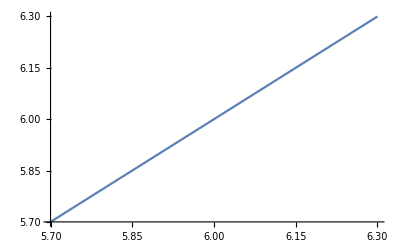

```mathematica
Plot[bprof[x],{x,xmin,xmax}]
```

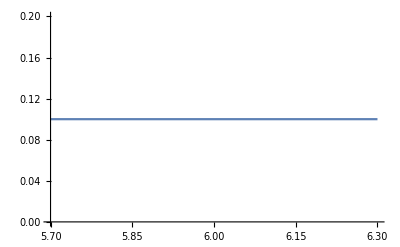

```mathematica
Plot[tprof[x],{x,xmin,xmax}]
```

## Initialization

#### Magnetic field,Density and Temperature Profiles

```mathematica
bprof[x_]:=If[Abs[(BXmax-BXmin)/BXmax]>10^-6,BXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(BXmax-BXmin),BXmin];
```

```mathematica
nprof[x_]:=If[Abs[(nXmax-nXmin)/nXmax]>10^-6,nXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(nXmax-nXmin),nXmin];
```

```mathematica
tprof[x_]:=If[Abs[(TXmax-TXmin)/TXmax]>10^-6,TXmin+(x-xProfileMin)/(xProfileMax-xProfileMin)(TXmax-TXmin),TXmin];
```

```mathematica
αHcut[B_,freq_, nz_,sgn_]:=(1-nz^2)×(1+sgn*2.79926 B/freq)
```

## Trapezoidal Rule List Integral

```mathematica
TrapezInt[v_List]:=

(* Integral using trapezoidal rule of a list of {x,f(x)} pairs.
	v is a list of the form {{x1,f(x1)},{x2,f(x2)},...}  	*)
	
	Module[{int=0},
	Do[int=int+(v[[i+1,1]]-v[[i,1]])*(v[[i+1,2]]+v[[i,2]])/2.,
	{i,1,Length[v]-1}];
	int]
```